```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="response"}
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
theoryDataT0=Import[StringJoin["theory-lT",".json"], "RawJSON"];
theoryDataT=Import[StringJoin["theory-hT",".json"], "RawJSON"];

a1Data0=Import[StringJoin["a1-",suffix,"-alphas=0.05,0.08",".json"], "RawJSON"];
a2Data0=Import[StringJoin["a2-",suffix,"-alphas=0.05,0.08",".json"], "RawJSON"];
a1Data1=Import[StringJoin["a1-",suffix,"-alphas=0.1,0.3",".json"], "RawJSON"];
a2Data1=Import[StringJoin["a2-",suffix,"-alphas=0.1,0.3",".json"], "RawJSON"];
a1Data2=Import[StringJoin["a1-",suffix,"-alphas=0.5,0.7",".json"], "RawJSON"];
a2Data2=Import[StringJoin["a2-",suffix,"-alphas=0.5,0.7",".json"], "RawJSON"];
```

Suffix: response

Sample sizes: 60

60

{{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{False,True},{False,True},{False,True}}

{-10.,-6.,-2.,2.,6.,10.}

-5.06253

-4.62873

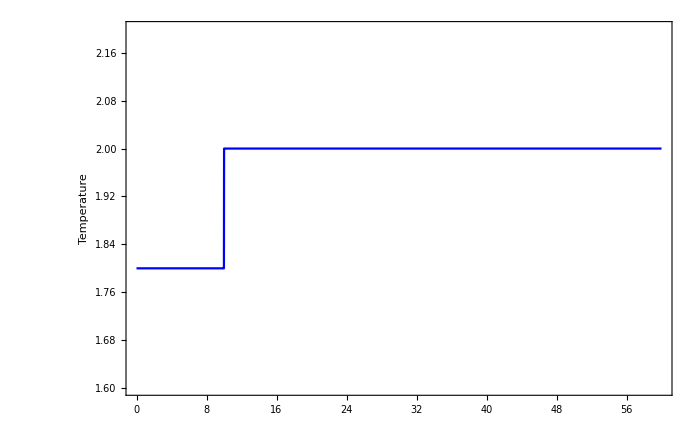

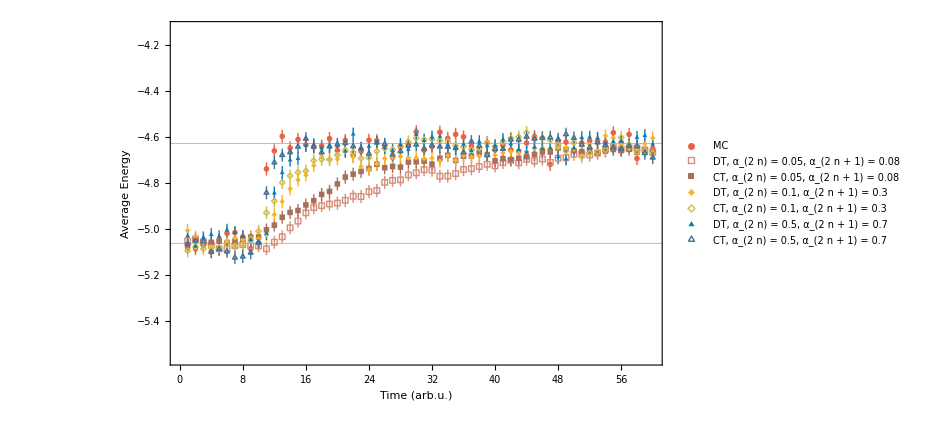

-Graphics-

Null

Null

```mathematica
{engyMc, engyA1n0,engyA2n0, engyA1n1,engyA2n1, engyA1n2,engyA2n2}=#["energy_sample"]&/@{mcData, a1Data0,a2Data0, a1Data1,a2Data1, a1Data2,a2Data2};
Row@{"Sample sizes: ",sampleSize=Length[engyMc]}
Assert@And[
sampleSize==Length[engyA1n0],
sampleSize==Length[engyA2n0],
sampleSize==Length[engyA1n1],
sampleSize==Length[engyA2n1],
sampleSize==Length[engyA1n1],
sampleSize==Length[engyA2n1]
] 
T0 = mcData["T0"];
T = mcData["T"];
timeT0 = mcData["Length T0"] / mcData["frame_step T0"];
time = Length[engyMc]
Assert@And ={
T0 == #["T0"] &/@{a1Data0, a2Data0},
T0 == #["T0"] &/@{a1Data1, a2Data1},
T0 == #["T0"] &/@{a1Data2, a2Data2},
T == #["T"]  &/@{a1Data0, a2Data0},
T == #["T"]  &/@{a1Data1, a2Data1},
T == #["T"]  &/@{a1Data2, a2Data2},
time == Length[#]&/@{engyA1n0, engyA2n0},
time == Length[#]&/@{engyA1n1, engyA2n1},
time == Length[#]&/@{engyA1n1, engyA2n1},
timeT0 == #["Length T0"] &/@{a1Data0, a2Data0},
timeT0 == #["Length T0"] &/@{a1Data1, a2Data1},
timeT0 == #["Length T0"] &/@{a1Data2, a2Data2}
}

energyLevel = theoryDataT["energy_level"]
engyTheoryT0 = Total[theoryDataT0["energy_probs"] * energyLevel]
engyTheoryT = Total[theoryDataT["energy_probs"]*energyLevel]

colors = Table[ColorData[28][i],{i,13}];
baseStyle1 = Directive[Black, FontFamily->"Arial", FontSize->16];
baseStyle2 = Directive[Blue, FontFamily->"Arial", FontSize->16];
baseStyle3 = Directive[Red, FontFamily->"Arial", FontSize->16];

from=20;to=-20;
temperaturePlot=Plot[
Piecewise[{{T0,x<timeT0},{T,x>timeT0}}],{x,0,time},
PlotRange->{Automatic,  {T0 - 0.2, T + 0.2}},
PlotStyle->Blue,
Axes -> False,
Frame->{{True,False},{False,False}},
FrameStyle->{{Append[baseStyle2,Thickness@0.004],None},{None, None}},
FrameLabel->{{"Temperature",""},{"",""}}, 
ImageSize-> 700]

markers = {●, □, ■, ◆, ◇, ▲, △};

{stdMc, stdA1n0, stdA2n0, stdA1n1, stdA2n1, stdA1n2, stdA2n2} = #["std_engy"]&/@ {mcData, a1Data0,a2Data0, a1Data1,a2Data1, a1Data2,a2Data2} / Sqrt[10000];

For [i=1 , i<=time, i++,
engyMc[[i]] = Around[engyMc[[i]], stdMc[[i]]];
engyA1n0[[i]] = Around[engyA1n0[[i]], stdA1n0[[i]]];
engyA2n0[[i]] = Around[engyA2n0[[i]], stdA2n0[[i]]];
engyA1n1[[i]] = Around[engyA1n1[[i]], stdA1n1[[i]]];
engyA2n1[[i]] = Around[engyA2n1[[i]], stdA1n1[[i]]];
engyA1n2[[i]] = Around[engyA1n2[[i]], stdA1n2[[i]]];
engyA2n2[[i]] = Around[engyA2n2[[i]], stdA2n2[[i]]];
]

energyPlot=ListPlot[{engyMc, engyA1n0, engyA2n0, engyA1n1, engyA2n1, engyA1n2, engyA2n2},
PlotRange->{Automatic, {engyTheoryT0 -0.5,engyTheoryT + 0.5}},
PlotStyle->colors,
PlotMarkers->markers,
PlotLegends-> {"MC", "DT, α_(2  n) = 0.05, α_(2  n + 1) = 0.08", "CT, α_(2  n) = 0.05, α_(2  n + 1) = 0.08", "DT, α_(2  n) = 0.1, α_(2  n + 1) = 0.3", "CT, α_(2  n) = 0.1, α_(2  n + 1) = 0.3", "DT, α_(2  n) = 0.5, α_(2  n + 1) = 0.7", "CT, α_(2  n) = 0.5, α_(2  n + 1) = 0.7"},
Axes->False,
GridLines->{{}, {engyTheoryT0, engyTheoryT}},
GridLinesStyle->Directive[colors[[11]], Thick],
Frame->{{True,False},{True,False}},
FrameStyle->{{Append[baseStyle3,Thickness@0.004],None},{Append[baseStyle1,Thickness@0.004],None}},
FrameLabel->{{"Average Energy",""},{"Time (arb.u.)",""}}, 
ImageSize->700]
```